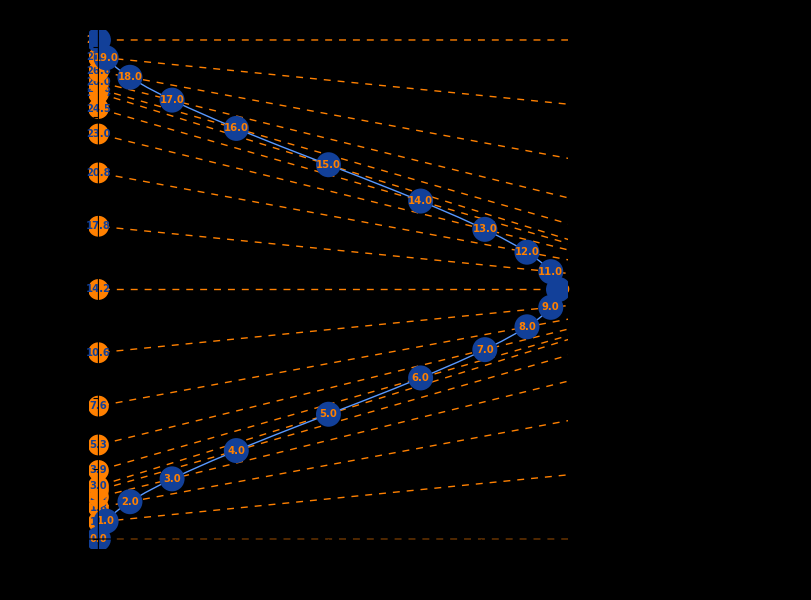
The Twin (Quasi)Paradox
-Graphics-
Profile: +0.3 ly/year^2 (≈ 0.29 g) to 5 yr; -0.3 ly/year^2 (≈ -0.29 g) to 15 yr; 0.3 ly/year^2 (≈ 0.29 g) to 20 yr.
At τ = 20 yr, stay-at-home age from simultaneity ≈ 28.39 yr (older by 8.39 yr).
Caveat: this “age” depends on the traveler’s simultaneity choice; relativity has no global now.

```mathematica
(* constants *)
  g = 9.80665; c = 299792458; yearSec = 365.25*24*3600;

  (* scenario: {tauStart, tauEnd, accelLyPerYear2} *)
  scenario = {{0, 5, 0.3}, {5, 15, -0.3}, {15, 20, 0.3}};

  (* numeric acceleration *)
  Clear[aFun];
  aFun[t_?NumericQ] := N@Piecewise[({#3, #1 <= t < #2} &) @@@ scenario, 0];

  (* solver *)
  solve[tauMax_] := Module[{sol},
    sol = NDSolveValue[
      {
       x'[τ] == Sinh[η[τ]],
       t'[τ] == Cosh[η[τ]],
       η'[τ] == aFun[τ],
       x[0.] == 0., t[0.] == 0., η[0.] == 0.
      },
      {x, t, η}, {τ, 0., tauMax},
      Method -> {"EquationSimplification" -> "Residual", "DiscontinuityProcessing" -> False}
    ];
    <|"x" -> sol[[1]], "t" -> sol[[2]], "eta" -> sol[[3]], "tauMax" -> tauMax|>
  ];

  (* plot builder with manual legend *)
  figure[tauMax_: 20, n_: 20] := Module[
    {sol = solve[tauMax], tauMarks, pts, v, b, lines, labels, homeAge, deltaAge, legend, plot},
    tauMarks = Subdivide[0., tauMax, n];
    pts = {sol["x"][#], sol["t"][#]} & /@ tauMarks;
    v[t_] := Tanh[sol["eta"][t]];
    b[t_] := sol["t"][t] - v[t]*sol["x"][t];
    lines = Table[
      With[{vv = v[t], bb = b[t]}, {
        {Orange, Dashed}, Line[{{-1, vv*(-1) + bb}, {10, vv*10 + bb}}],
        {Orange, PointSize[0.025]}, Point[{0, bb}],
        Text[Style[NumberForm[bb, {4, 1}], DarkBlue, 10, Bold], {0, bb}]
      }],
      {t, tauMarks}
    ] // Flatten;
    labels = MapThread[
      Text[Style[NumberForm[#1, {4, 1}], Orange, 10, Bold], #2] &,
      {tauMarks, pts}
    ];
    homeAge = b[tauMax]; deltaAge = homeAge - tauMax;

    legend = Placed[
      SwatchLegend[
        {
         Directive[Thick, RGBColor[0.35, 0.6, 1]],
         Directive[DarkBlue, PointSize[0.03]],
         Directive[Orange, Dashed],
         Directive[Orange, PointSize[0.025]]
        },
        {
         "Traveler worldline",
         "Equal Δτ markers (1 yr)",
         "Simultaneity line",
         "t-axis intercept"
        },
        LegendMarkers -> {
          {Graphics[{Line[{{0, 0}, {1, 0}}]}], 20},
          {Graphics[{Disk[{0, 0}, 1]}], 12},
          {Graphics[{Line[{{0, 0}, {1, 0}}]}], 20},
          {Graphics[{Disk[{0, 0}, 1]}], 12}
        },
        LabelStyle -> Directive[White, 12],
        LegendFunction -> (Framed[#, Background -> Black, FrameStyle -> Gray, FrameMargins -> 8] &)
      ],
      {Right, 0.85}
    ];

    plot = ParametricPlot[{sol["x"][τ], sol["t"][τ]}, {τ, 0, tauMax},
      PlotStyle -> {Thick, RGBColor[0.35, 0.6, 1]},
      AxesLabel -> {"x (ly)", "t (yr)"},
      BaseStyle -> 14,
      PlotRange -> {{-1, 10}, {0, All}},
      AspectRatio -> 1,
      ImageSize -> 600,
      Prolog -> lines,
      Epilog -> {{DarkBlue, PointSize[0.03], Point[pts]}, labels},
      Background -> Black
    ];

    Column[
      {
        Style["The Twin (Quasi)Paradox", White, 20, Bold],
        Legended[plot, legend],
        Style[
          Column[{
            Row[{
              "Profile: +", scenario[[1, 3]], " ly/year^2 (≈ ", NumberForm[scenario[[1, 3]]*(c/yearSec)/g, {3, 2}],
              " g) to 5 yr; ", scenario[[2, 3]], " ly/year^2 (≈ ", NumberForm[scenario[[2, 3]]*(c/yearSec)/g, {3, 2}],
              " g) to 15 yr; ", scenario[[3, 3]], " ly/year^2 (≈ ", NumberForm[scenario[[3, 3]]*(c/yearSec)/g, {3, 2}],
              " g) to 20 yr."
            }],
            Row[{
              "At τ = ", tauMax, " yr, stay-at-home age from simultaneity ≈ ",
              NumberForm[homeAge, {5, 2}], " yr (older by ", NumberForm[deltaAge, {4, 2}], " yr)."
            }],
            "Caveat: this “age” depends on the traveler’s simultaneity choice; relativity has no global now."
          }, Spacings -> 0.3],
          White, 12, LineSpacing -> {1.2, 0}, Alignment -> Center
        ]
      },
      Alignment -> Center,
      Background -> Black,
      Spacings -> {Automatic, 0.6}
    ]
  ];

  (* run *)
  figure[]
```